# Optimal Percolation Concentration for Finding Multiple Spanning Clusters

## Sam Keller and Milan Cvitkovic

## Section 01: Introduction

In this notebook, our group hopes to explore the probability of finding multiple spanning clusters in a given peroclation cluster. We hope to find a probability distribution for finding multiple spanning clusters over a range of occupied-site concentrations which, once plotted, will show us the concentration for which it is most probable that multiple spanning clusters appear. 

To do this, we will first use the site percolation program and the cluster labeling program given in the book-in-progress “Computer Simulations with Mathematica and Java” by Paul Wellin and Todd Gayley. This will allow us to create a lattice of sites having values of 1 (occupied) or 0 (not occupied).  Next we will identify all the unique clusters in the lattice using the Hoshen-Kopelman algorithm. Finally, we will scan the edges of the lattice to find common labels in either the first and last row or first and last column - if there are matching label sites in either of these it will tell us whether there is a spanning cluster, and if there are multiple matching labels we know we have multiple spanning clusters. 

Once we have this code working, we can run this module on a range of concentration values and run it many times for each concentration value. For each of them, we can output a probability of how likely it is that we find multiple spanning clusters for that particular concentration value by dividing the number of times we find multiple spanning clusters by the total number of tries done for this concentration value. Done over a whole range of concentration values, this algorithm will produce a long list of lists, with each sublist being of the form {concentration value, prob. of finding multiple spanning clusters}. Then, we can plot this list of lists to get a distribution which will find us the optimal concentration for which it is most probable that we find multiple spanning clusters! Effectively, we will have found the concentration threashold for multiple spanning clusters.

We expect that this optimal concentration value will be above the percolation threashold of p=0.59, but not too much higher since at high concentration values, distinct clusters are likely to bond together into a single cluster. 

The applications of this seem interesting because having multiple spanning clusters would have a drastic effect on the physical properties of the lattice and how percolation occurs in the lattice.

## Section 02: Needed Packages

Didn’t need any!

## Section 03: Site Percolation Program

Here is the Site Percolation Program from the new version of the CSM book. We’ll use this to make a percolation cluster

#### Code

```mathematica
Clear[sitePercolation]
sitePercolation[p_Real,m_Integer]:=Table[Floor[1+p-RandomReal[]],{m},{m}];
```

#### Code Check

```mathematica
cluster=sitePercolation[0.4,10];
cluster//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

It works! Let’s now work on labeling clusters

## Section 04: Cluster Labeling Program

Now, we will use the cluster labeling program provided by Wellin and Gayley in their new CSM book. We know from our homework assignment that this program has the potential to mislabel clusters... but because this is the best implementation of the H-K algorithm that we have right now, it will have to do.

#### Code

```mathematica
Clear[ClusterLabel]
ClusterLabel[sp_List] := Module[{u, ul, ulp, uN, uW, ulN, ulW, len = Length[sp], rules1, rules2, labels},
  u = PadLeft[sp, {len + 1, len + 1}];
  ul = u /. 1 -> 0;
  ulp = {};
  Do[
   uN := u[[q - 1, k]];
   uW := u[[q, k - 1]];
   ulN := ul[[q - 1, k]];
   ulW := ul[[q, k - 1]];
   Which[u[[q, k]] == 1 && uN == 1 && uW == 1 && ulN =!= ulW, ul[[q, k]] = Min[ulp[[ulW]], ulp[[ulN]]]; ulp[[Max[ulp[[ulW]], ulp[[ulN]]]]] = Min[ulp[[ulW]], ulp[[ulN]]], u[[q, k]] == 1 && uN == 1, ul[[q, k]] = ulN, u[[q, k]] == 1 && uW == 1, ul[[q, k]] = ulW, u[[q, k]] == 1, ul[[q, k]] = Max[ul] + 1;
    AppendTo[ulp, Max[ul]]],
   {q, 2, len + 1}, {k, 2, len + 1}];
  rules1 = Thread[Range[Length[ulp]] -> ulp];
  labels = ulp //.rules1;
  rules2 = Thread[Union[labels] -> Range[Length[Union[labels]]]];
  ul //. rules1 /. rules2]
```

#### Code Check

```mathematica
labelMatrix=ClusterLabel[cluster];
labelMatrix//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0 | 3 | 0 | 0 | 4
0 | 0 | 0 | 5 | 0 | 6 | 0 | 0 | 0 | 7 | 0
0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 7 | 0
0 | 8 | 0 | 9 | 0 | 10 | 10 | 0 | 0 | 7 | 7
0 | 0 | 11 | 0 | 10 | 10 | 0 | 10 | 0 | 0 | 0
0 | 0 | 0 | 10 | 10 | 10 | 10 | 10 | 0 | 0 | 12
0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 13 | 0
0 | 14 | 0 | 0 | 15 | 0 | 16 | 16 | 0 | 0 | 17
0 | 14 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 16 | 16 | 16 | 0 | 0 | 0 | 0)

Looks good! It labels all of the different clusters with differnet numbers.

## Section 05: Finding Two Spanning Clusters in Percolation Clusters

Now we need to write a module that will find the number of spanning clusters for a given concentration value. To do this, our module will take in a pStart and an pEnd, along with a pStep, that will step through all the values betwen pStart and pEnd and produce a percolating cluster for each concentration. With each percolating cluster, we'll make a labeled lattice that has the labeled clusters in it. In this lattice, we will pull out the first and last row and check for any similar numbers. If there are similar numbers, then we have spanning clusters! Then we'll return a list of lists, where each sublist has the p value and the number of spanning clusters in it. We'll also check for horizontal spanning clusters by making a second labeled lattice, which is the transpose of the first one (so that the rows and columns are switched), and we'll perform the same check for that lattice.

Because of the way ClusterLabel works, there is always a row and column of 0s at the beginning of the labeled cluster-- this means that we'll always have one spannign cluster, beacuse it will be comprisd of 0s. So, when we check for multiple spanning clusters, we'll be looking for at least 3 (one of which is 0s and the rest make up real spanning clusters).

#### Code Development

To run this type of module, we'll need to make use the Intersection function to check the first and last row of a labeled cluster lattice for any common clusters.

```mathematica
Intersection[{1,2,3,4,5},{3,6,7,8,9}]
```

{3}

As we can see, if those two lists had been our first and last rows, Intersection produced just a 3, signaling that there's only one spanning cluster and that it is a bunch of 3s

#### Code

```mathematica
Clear[findSpanningClusters]
findSpanningClusters[pStart_,pEnd_,pStep_,latticeEdge_]:=
Module[
{pList = {},currentLattice,labelLattice,labelLattice2,i,p},

For[p=pStart,p≤pEnd,p=p+pStep,(
currentLattice=Table[Floor[1+p-RandomReal[]],{latticeEdge},{latticeEdge}];(* This creates the Percolating Cluster *)
labelLattice=ClusterLabel[currentLattice];
labelLattice2=Transpose[labelLattice];
If[Length[Intersection[labelLattice[[2]],labelLattice[[-1]]]]> 2 ,
AppendTo[pList,{p,Length[Intersection[labelLattice[[2]],labelLattice[[-1]]]]-1}]
,If[Length[Intersection[labelLattice2[[2]],labelLattice2[[-1]]]]> 2,

AppendTo[pList,{p,Length[Intersection[labelLattice2[[2]],labelLattice2[[-1]]]]-1}];

]

]
)
];

pList

]
```

#### Code Check

```mathematica
findSpanningClusters[0.5,0.7,0.01,20]
```

{{0.61,2}}

Looks like it worked! For one concentration value, p=0.63, we got two spanning clusters in the percolating cluster! So, it doesn't look like it's likely to have multiple spanning clusters, but it is possible!

## Section 06: Finding a Distribution of The Probabilities of Finding Multiple Spanning Clusters For Different Concentration Values

Now, we want to a slightly ldifferent thing-- we want to run the same basic algorithm, but for each concentation value, we want to produce a large number of percolating clusters and determine in how many of those clusters are there multiple spanning clusters. To do this, we'll add an extra For loop in our program that runs the Cluster Labeling program a large number of times. Each time there are multiple spanning clusters, we'll add one to this index that we call "numMultiple." Then, after we've made a lot of clusters for one concentration value, we'll calculate the number of occurances of multple spanning clusters divided by the number of percolating clusters created, effectively giving us a probability of how likely it is, for a single concentration value, that multiple spanning clusters appear. We'll then make a list of all of these probabilities and their associated concentration values and return the whole list.

#### Code

```mathematica
Clear[findSpanningClusters2]
findSpanningClusters2[pStart_,pEnd_,pStep_,runs_,latticeEdge_]:=
Module[
{numMultiple=0,currentLattice,labelLattice,labelLattice2,i,probability,p,pList={}},

For[p=pStart,p≤pEnd,p=p+pStep,(
numMultiple=0;
For[i=1,i≤runs,i++,(
currentLattice=Table[Floor[1+p-RandomReal[]],{latticeEdge},{latticeEdge}];
labelLattice=ClusterLabel[currentLattice];
labelLattice2=Transpose[labelLattice];
If[Length[Intersection[labelLattice[[2]],labelLattice[[-1]]]]>2 ,
numMultiple++;
,If[Length[Intersection[labelLattice2[[2]],labelLattice2[[-1]]]]>2,
numMultiple++;
];

];
);
];
probability=numMultiple/runs;
AppendTo[pList,{p,probability}];
);
];

pList
];
```

#### Code Check

```mathematica
findSpanningClusters2[0.6,0.7,0.01,100,30]
```

{{0.6,3/100},{0.61,1/100},{0.62,1/25},{0.63,1/100},{0.64,1/50},{0.65,3/100},{0.66,1/100},{0.67,1/50},{0.68,1/100},{0.69,0},{0.7,1/50}}

Looks like it works!

### Code Run For Real!

Now, we'll run our simulation on cluster sizes of 30, where we have a range of concentration values that range from 0.4 to 0.8. For each concentration value, we'll make 5000 percolating clusters and look for spanning clusters-- the number of clusters that produce 2 spanning clusters divided by the total number of clusters made will produce a probability of finding multiple spanning clusters!

```mathematica
data=findSpanningClusters2[0.4,0.8,0.01,5000,30]
```

{{0.4,0},{0.41,0},{0.42,0},{0.43,0},{0.44,0},{0.45,0},{0.46,0},{0.47,0},{0.48,0},{0.49,0},{0.5,0},{0.51,0},{0.52,0},{0.53,0},{0.54,1/1000},{0.55,3/2500},{0.56,3/1000},{0.57,11/1250},{0.58,6/625},{0.59,63/5000},{0.6,17/1000},{0.61,1/50},{0.62,111/5000},{0.63,29/1250},{0.64,107/5000},{0.65,43/2500},{0.66,43/2500},{0.67,31/2500},{0.68,9/1000},{0.69,13/2500},{0.7,2/625},{0.71,9/5000},{0.72,1/1000},{0.73,1/2500},{0.74,1/5000},{0.75,0},{0.76,0},{0.77,0},{0.78,0},{0.79,0},{0.8,0}}

Looks like we found a lot of clusters that had multiple spanning clusters... let's ListPlot this data to see if we can get some sort of recognizable distribution

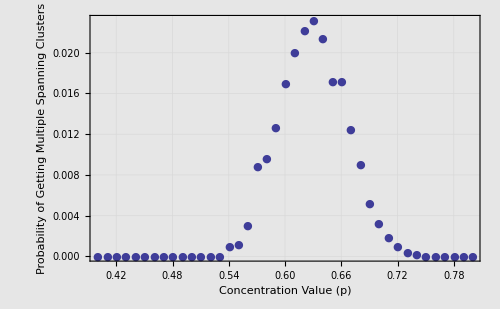

```mathematica
ListPlot[data,Frame->True,FrameLabel->{"Concentration Value (p)","Probability of Getting Multiple Spanning Clusters","Probability of Finding Two Spanning Clusters as a Function of Concentration",""},PlotMarkers->{Automatic,Small},GridLines->Automatic,ImageSize->500,Background->GrayLevel[0.9]]
```

Wow!! Check out that distribution! We clearly have an optimal concentration value at p=0.63. This means that this is the value at which the probability of finding multiple spanning clusters is highest.

Now let’s see what happens when we hone in on the threashold. We’ll do the same run but for a range of probabilities from 0.6 and 0.66, since we know that the critical probability probably lies within that range

```mathematica
data2=findSpanningClusters2[0.6,0.66,0.002,5000,30];
data3=findSpanningClusters2[0.6,0.66,0.002,5000,60];
```

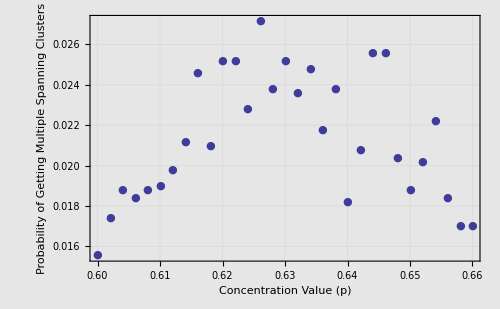

```mathematica
ListPlot[data2,Frame->True,FrameLabel->{"Concentration Value (p)","Probability of Getting Multiple Spanning Clusters","Probability of Finding Two Spanning Clusters as a Function of Concentration",""},PlotMarkers->{Automatic,Small},GridLines->Automatic,ImageSize->500,Background->GrayLevel[0.9]]
ListPlot[data3,Frame->True,FrameLabel->{"Concentration Value (p)","Probability of Getting Multiple Spanning Clusters","Probability of Finding Two Spanning Clusters as a Function of Concentration",""},PlotMarkers->{Automatic,Small},GridLines->Automatic,ImageSize->500,Background->GrayLevel[0.9]]
```

While there is a lot more error in the probabilities (not shown because there is no way to extrapolate error bars from our data), the maximum appears to be about 0.63

Also, to check whether the concentration at which there is a maximum likelihood of finding multiple spanning clusters depends on lattice size, we ran the same simulation but using a lattice size of 60x60 (4 times the size used to generate the above two distributions):

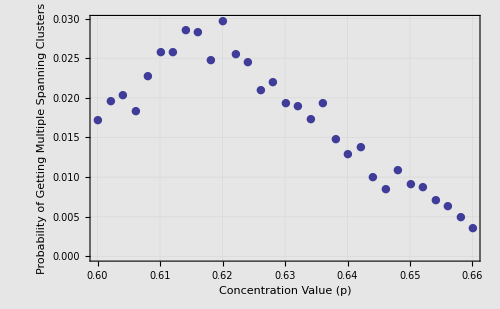

We can see that, indeed, lattice size has an affect on the probability distribution - the concentration at which there is a maximum likelihood of finding multiple spanning clusters appears to have moved from ~0.63 with a 20x20 lattice to ~0.615 with a 6060 lattice.

## Section 08: Conclusions

After having run this simulation for a long period of time using a 20x20 lattice, we ended up with a list of concentration values and the associated probability of finding multiple spanning clusters. Our data produced a nice probability distribution which has a maximum value around p=0.63. This is the concentration value for which it is most probable to find multple spanning clusters in a percolation cluster.  It's not too surprising that this value is not much larger than the percolation threashold for a single percolation cluster-- below the threashold, because it's improbable to get a single spanning cluster, it's even more improbable to get two distinct spanning clusters. However, if the concentration value is too large, then multiple spanning clusters would likely join at some place in the lattice and combine to make one spanning cluster. 

When using a lattice of size 60x60, the concentration at which there is a maximum likelihood of finding multpiple spanning clusters changes to p = 0.615.  Though we only had time to test two lattice sizes, the difference in p values for these two different lattices indicates that there is a finite size effect for finding multiple spanning clusters.